# Postelje Ameriških Bolnicah

## pridobivanje podatkov

Podatke sem pridobil iz Wolfram data repository

```mathematica
podatki = ResourceData["Hospital Beds Per US State"]
```

## Alabama

Najprej si bomo pogledali, kaj se dogaja v Alabami.

```mathematica
Alabama = Select[podatki,#["Location"]== LinguisticAssistant&]
```

```mathematica
NeprofitnePosteljeAlabama = %[[1]]["NonProfitBedsPer1000Inhabitants"]
```

```mathematica
TimeSeries[…]
```

TimeSeriesWindow[TotalBedsPer1000Inhabitants][TotalBedsPer1000Inhabitants]

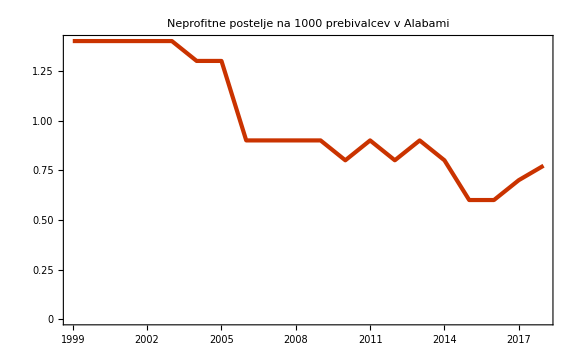

```mathematica
DateListPlot[NeprofitnePosteljeAlabama, PlotLabel->"Neprofitne postelje na 1000 prebivalcev v Alabami", PlotTheme->"Web", ImageSize->Large]
```

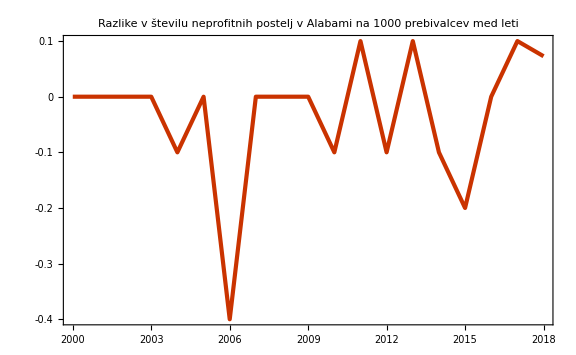

```mathematica
DateListPlot[Differences[NeprofitnePosteljeAlabama], PlotLabel->"Razlike v številu neprofitnih postelj v Alabami na 1000 prebivalcev med leti", PlotTheme->"Web", ImageSize->Large]
```

## Kentucky

```mathematica
Kentucky = Select[podatki,#["Location"]== LinguisticAssistant&]

KvotaNa1000PrebivalcevKentucky = {3.96*10^6, 3.98*10^6, 4.06*10^6,4.09*10^6,4.11*10^6,4.14*10^6,4.18*10^6,4.21*10^6,4.25*10^6,4.28*10^6,4.31*10^6,4.33*10^6,4.37*10^6,4.38*10^6,4.40*10^6,4.41*10^6,4.42*10^6,4.43*10^6,4.45*10^6,4.46*10^6} / 1000
```

```mathematica
TotalBedsPer1000Kentucky = %[[1]]["TotalBedsPer1000Inhabitants"]
```

TimeSeries[…]

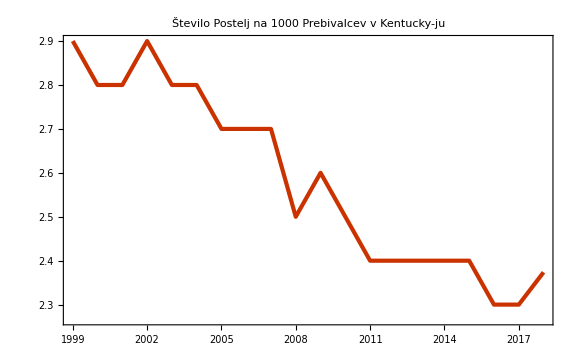

```mathematica
g1 = DateListPlot[TotalBedsPer1000Kentucky, PlotLabel->"Število Postelj na 1000 Prebivalcev v Kentucky-ju", PlotTheme->"Web", ImageSize->Large]
```

## Florioda

```mathematica
Florida = Select[podatki,#["Location"]== LinguisticAssistant&]
```

TimeSeries[…]

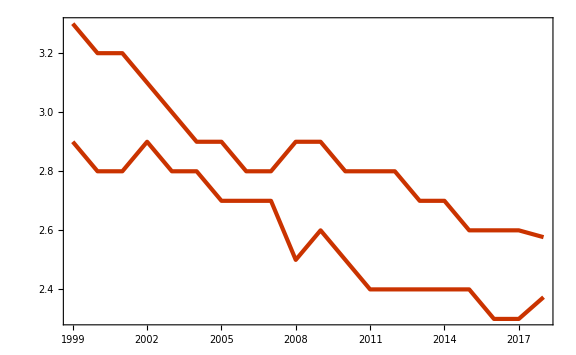

```mathematica
TotalBedsPer1000Florida = %[[1]]["TotalBedsPer1000Inhabitants"]
Show[g2,g1, PlotRange->All]
```

Graf prikazuje Skupno število postelj v zdravstvu na 1000 Prebivalcev v Kentuckyju in Floridi.